```mathematica
SetDirectory["C:\\Users\\Georg\\Desktop\\figs"];
<<"CustomTicks.m"
```

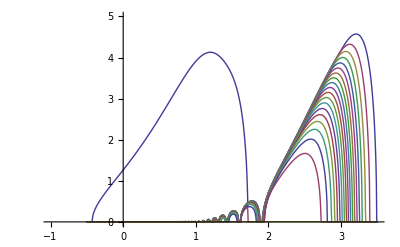

```mathematica
a=.
n=20;
z=1/n;
ϵ=1/2;
λ=0.;
μ=10^a;
h=-1;
ω=Table[-1,{i,1,n}]~Join~Table[+1,{i,1,n}];
g=Table[h μ,{i,1,n}]~Join~Table[-h (1+ϵ) μ,{i,1,n}]/n;
u=.
uu=Table[(1-n z)/2+z(i-1/2),{i,1,n}]~Join~Table[(1-n z)/2+z(i-1/2),{i,n,1,-1}];
m=Table[KroneckerDelta[i,j] (ω[[i]]+(ϵ μ+λ) uu[[i]])-(uu[[i]]+uu[[j]]) g[[j]],{i,1,2 n},{j,1,2 n}];
pmax=n;
MySort[m_]:=Module[{s},s=Sort[Im[Eigenvalues[m]],Greater];Table[s[[i]],{i,1,pmax}]]
kap=Table[{a}~Join~MySort[m],{a,-0.5,3.5,0.005}];
len=Length[kap];
ListLinePlot[Table[Table[{kap[[i,1]],kap[[i,1+j]]},{i,1,len}],{j,1,pmax}],PlotRange->{{-1,3.5},{0,5}}]
```

```mathematica
n=20;
z=1/n;
ϵ=1/2;
λ=0.;
μ=.
h=-1;
ω=Table[-1,{i,1,n}]~Join~Table[+1,{i,1,n}];
g=Table[h μ,{i,1,n}]~Join~Table[-h (1+ϵ) μ,{i,1,n}]/n;
u=.
uu=Table[(1-n z)/2+z(i-1/2),{i,1,n}]~Join~Table[(1-n z)/2+z(i-1/2),{i,n,1,-1}];
m=Table[KroneckerDelta[i,j] (ω[[i]]+(ϵ μ+λ) uu[[i]])-(uu[[i]]+uu[[j]]) g[[j]],{i,1,2 n},{j,1,2 n}];
pmax=n;
MySort[m_]:=Module[{s},s=Sort[Im[Eigenvalues[m]],Greater];Table[s[[i]],{i,1,pmax}]]
```

```mathematica
μ=45.;
MySort[m]
```

{2.36176,0.318251,0.318162,0.317418,0.317267,0.315626,0.315458,0.313264,0.312018,0.310179,0.306452,0.306349,0.30174,0.297461,0.296253,0.28911,0.281996,0.270693,0.250255,0}

```mathematica
Eigenvalues[m]
Ω1=Part[Eigenvalues[m],32]
```

{22.4858,21.0448+0.270693 ⅈ,21.0448-0.270693 ⅈ,19.9518+0.28911 ⅈ,19.9518-0.28911 ⅈ,18.8306+0.296253 ⅈ,18.8306-0.296253 ⅈ,17.7009+0.30174 ⅈ,17.7009-0.30174 ⅈ,16.5677+0.306349 ⅈ,16.5677-0.306349 ⅈ,15.4329+0.310179 ⅈ,15.4329-0.310179 ⅈ,14.2971+0.313264 ⅈ,14.2971-0.313264 ⅈ,13.1606+0.315626 ⅈ,13.1606-0.315626 ⅈ,12.0233+0.317267 ⅈ,12.0233-0.317267 ⅈ,10.8852+0.318162 ⅈ,10.8852-0.318162 ⅈ,9.74614+0.318251 ⅈ,9.74614-0.318251 ⅈ,8.60598+0.317418 ⅈ,8.60598-0.317418 ⅈ,7.46437+0.315458 ⅈ,7.46437-0.315458 ⅈ,6.32083+0.312018 ⅈ,6.32083-0.312018 ⅈ,5.17463+0.306452 ⅈ,5.17463-0.306452 ⅈ,-3.41937+2.36176 ⅈ,-3.41937-2.36176 ⅈ,4.02459+0.297461 ⅈ,4.02459-0.297461 ⅈ,2.86855+0.281996 ⅈ,2.86855-0.281996 ⅈ,1.70122+0.250255 ⅈ,1.70122-0.250255 ⅈ,0.250614}

-3.41937+2.36176 ⅈ

```mathematica
n=20;
ϵ=1/2;
μ=45.;
Ω=Ω1;
h=-1;
i0=Sum[(-μ/(-1+ϵ μ ((i-1/2)/n) -Ω)+μ(1+ϵ)/(1+ϵ μ ((i-1/2)/n)-Ω))/n,{i,1,n}]
i1=Sum[((i-1/2)/n)(-μ/(-1+ϵ μ ((i-1/2)/n)-Ω)+μ(1+ϵ)/(1+ϵ μ ((i-1/2)/n)-Ω))/n,{i,1,n}]
i2=Sum[((i-1/2)/n)^2(-μ/(-1+ϵ μ ((i-1/2)/n)-Ω)+μ(1+ϵ)/(1+ϵ μ ((i-1/2)/n)-Ω))/n,{i,1,n}]
(h+i1)^2-i0 i2//FullSimplify
```

1.04826-0.143831 ⅈ

0.453322+0.0184136 ⅈ

0.282099+0.0195008 ⅈ

-4.44089×10^-16-2.46331×10^-16 ⅈ

```mathematica
b=1;
a=Last[Last[Last[Solve[(i1-h)aa+i2 b==0,aa]]]];
ω=0;
Q[ω_,u_]:=(a+b u)/(ω+(ϵ μ+λ)u-Ω)
ω=0;
rx=.
ry=.
eq1=(Re[Q[ω,0]]-rx)^2+(Im[Q[ω,0]]-ry)^2==(Re[Q[ω,1/2]]-rx)^2+(Im[Q[ω,1/2]]-ry)^2;
eq2=(Re[Q[ω,1]]-rx)^2+(Im[Q[ω,1]]-ry)^2==(Re[Q[ω,1/2]]-rx)^2+(Im[Q[ω,1/2]]-ry)^2;
ss=Solve[{eq1,eq2},{rx, ry}];
rx=Last[First[Last[ss]]];
ry=Last[Last[Last[ss]]];
p=(rx - I ry)/(rx^2+ry^2);
ω=.
Clear[Q]
Q[ω_,u_]:=p(a+b u)/(ω+(ϵ μ+λ)u-Ω)
Q[ω,u]//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

((4.10765+12.2679 ⅈ) ((-0.194245-0.010957 ⅈ)+u))/((3.41937-2.36176 ⅈ)+22.5 u+ω)

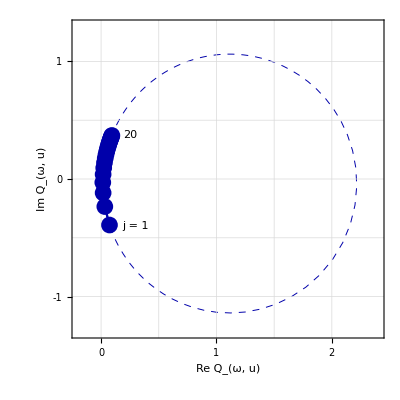

disvec2.eps

```mathematica
p1=ParametricPlot[{{Re[Q[1,u]],Im[Q[1,u]]}},{u,-15,10},PlotRange->{{-0.2,2.4},{-1.3,1.3}},AspectRatio->1,
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},
PlotStyle->{{AbsoluteThickness[0.7],Darker[Blue],Dashed},{AbsoluteThickness[0.7],Darker[Red],Dashed},{AbsoluteThickness[0.5],Black}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,GridLines->{{0,0.5,1,1.5,2},{-1,-0.5,0,0.5,1}},
Epilog-> {Inset["j = 1",{0.3,-0.4},{Center,Center}],Inset["20",{0.25,0.37},{Center,Center}]},
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style["Re Q_(ω, u)",14],Style["Im Q_(ω, u)",14]},
FrameTicks->{LinTicks[-1,3,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-1,3,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[-2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}];
v1=Table[{Re[Q[1,uu[[i]]]],Im[Q[1,uu[[i]]]]},{i,1,20}];
v2=Table[{Re[Q[-1,uu[[i]]]],Im[Q[-1,uu[[i]]]]},{i,21,40}];
p2=ListPlot[{v1},Axes->False,
PlotStyle->{{PointSize[0.03],Darker[Blue]}}];
p3=ListLinePlot[{v1},
PlotStyle->{{AbsoluteThickness[1.7],Darker[Blue]}},Axes->False];
plot1=Show[p1,p2,p3]
Export["disvec2.eps",plot1]
```